```mathematica
CompileOccTime[data_]:=Module[{fresult={},result,landparam,allq,newallq,dim,min,M=5},
landparam = data[[1]];
Do[
result = ConstantArray[{},M];
Do[
AppendTo[result[[sp]],landparam[[i]]];
allq = newallq=data[[i+1,sp]];
dim = Map[Length,allq];
min=Min[dim];
Do[
newallq[[l]]=allq[[l,-min;;]];
,{l,Length[dim]}];
AppendTo[result[[sp]],Mean[newallq]];
,{sp,M}];
AppendTo[fresult,result];
,{i,Length[data[[1]]]}];
fresult];
```

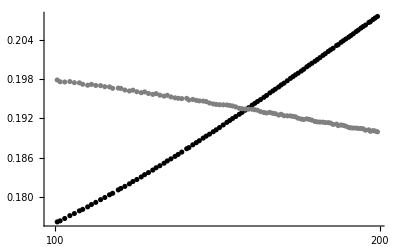

```mathematica
dd = Get["H:\\final_run_fig4b\\one_code\\task_2b_yes_agg_est_True_z_0_M_5_size_3_time_200_ca_1_dt_2_dq_0.05_rho_0.2_tau_1._rep_1"];

dat = dd[[2]];(*The first coordinate is for rho and tau*)
mG = mS1 =mS2 =mS3 =mS4 ={};
Do[
tg = dat[[1,npatch]];
ts1 = dat[[2,npatch]];
ts2 = dat[[3,npatch]];
ts3 = dat[[4,npatch]];
ts4 = dat[[5,npatch]];

AppendTo[mG,tg];
AppendTo[mS1,ts1];
AppendTo[mS2,ts2];
AppendTo[mS3,ts3];
AppendTo[mS4,ts4];

,{npatch,3*3}];
meanG = Mean[mG];
meanS1 = Mean[mS1];
meanS2 = Mean[mS2];
meanS3 = Mean[mS3];
meanS4 = Mean[mS4];
meanS = Mean[{meanS1,meanS2,meanS3,meanS4}];

fig0=ListLinePlot[{meanG, meanS},PlotStyle-> {Black,Gray}];
fig= ListLogLinearPlot[{meanG, meanS},PlotStyle-> {Black,Gray},PlotRange->All]
```